```mathematica
data = {{2.17382199142695,6.283184785},{2.17382199142697,6.283185414},{2.17382199142684,6.283186043}}
parabola = Fit[data,{1,x,x^2},x]
```

{{2.17382,6.28318},{2.17382,6.28319},{2.17382,6.28319}}

2.0944+0.963462 x+0.443211 x^2

```mathematica
b = 2.17382199142713;

N[-7.348375065062388+3.170993803389905 * b+1.4259617225198689*b^2-2*Pi]
```

7.35823×10^-7

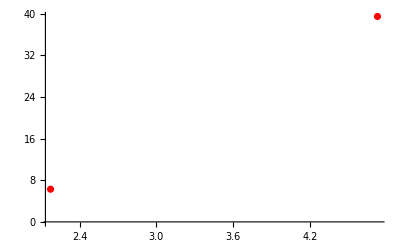

```mathematica
7.358231295384599*^-7

Show[ListPlot[data,PlotStyle->Red],Plot[{parabola},{x,2.17382,2.17383}]]
```

```mathematica
N[(5*10^-7*180/Pi *3600 *100/0.241)]
```

42.7935